```mathematica
SetDirectory[NotebookDirectory[]];
Get<<"data/SolutionVector2_Feb3";
SolutionVector01=SolutionVector2/.Null->Nothing;
BendTests=Import["data/201708_BendTests_SS_processed_data_Info.mat"];
Bendlabels=Import["data/201708_BendTests_SS_processed_data_Info.mat","Labels"]
BendTestAll=Import["data/201708_BendTests_SS_processed_data_Fw0.mat"];
BendlabelAll=Import["data/201708_BendTests_SS_processed_data_Fw0.mat","Labels"]
force= BendTestAll[[Position[BendlabelAll,"force"][[1,1]] ]];
dflctn= BendTestAll[[Position[BendlabelAll,"dflctn"][[1,1]] ]];
Bstif=Flatten[ BendTests[[Position[Bendlabels,"Bstif"][[1,1]] ]]];(*EI/L^3*)
Kcant=Flatten[ BendTests[[Position[Bendlabels,"Kcant"][[1,1]] ]]];
w0slp=Flatten[ BendTests[[Position[Bendlabels,"w0slp"][[1,1]] ]]];
w0star=Flatten[ BendTests[[Position[Bendlabels,"w0star"][[1,1]] ]]];
wsslp=Flatten[ BendTests[[Position[Bendlabels,"w_sslp"][[1,1]] ]]];
wsstar=Flatten[ BendTests[[Position[Bendlabels,"w_sstar"][[1,1]] ]]];
L=Flatten[ BendTests[[Position[Bendlabels,"L"][[1,1]] ]]];
SSpattern=Flatten[ BendTests[[Position[Bendlabels,"SSpattern"][[1,1]] ]]];
Pslip=Flatten@Position[SSpattern,True];
Pcontinue =Flatten@Position[SSpattern[[;;38]],False];
w0slpN=(w0slp/L)[[Pslip]];
w0starN=(w0star/L)[[Pslip]];
StageDis=(wsslp/L)[[Pslip]];
FailDis=(wsstar/L)[[Pslip]];
OblSlope=(Kcant/Bstif)[[Pslip]];
fw0All=Table[{dflctn[[i,j]]/L[[i]],force[[i,j]]/Bstif[[i]]/L[[i]]},{i,38},{j,Length@force[[i]]}];
fw0=fw0All[[Pslip]];
FailureIndex=Table[Length@Select[fw0[[i,;;,1]],0<#≤w0starN[[i]]&],{i,Length@w0starN}];
```

{Bstif,D,E,Fslp,Fstar,K_s,Kc_SE,Kcant,L,N_L,SSpattern,axL,dSstar,evbool,indx_fail,indx_slp,sD,s_L,w0slp,w0star,w_sslp,w_sstar}

{Fslp,Fstar,dflctn,dsplcmnt,force}

## Schematic:

μ = 0.0

### constant μ = 0.0

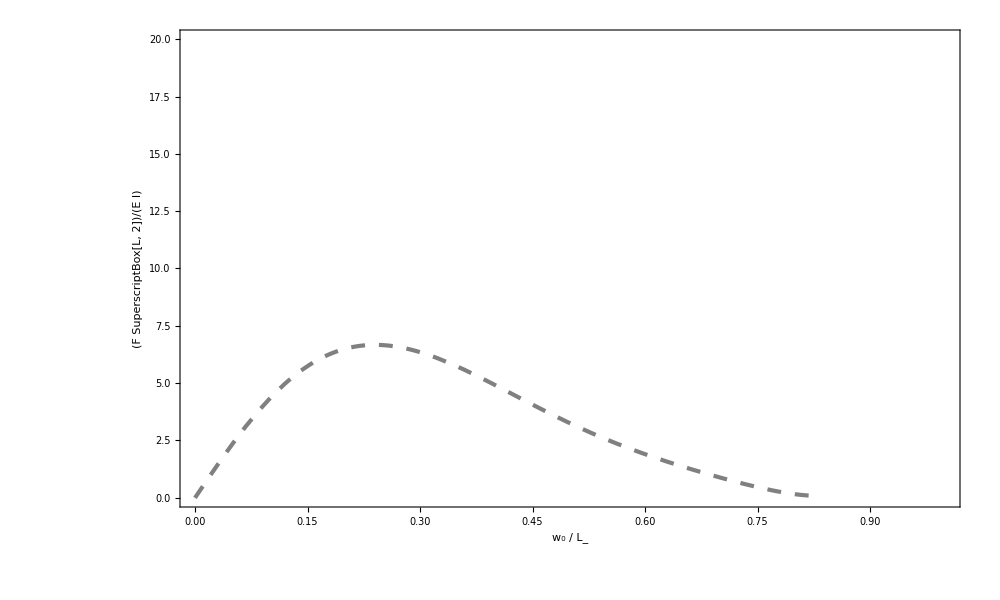

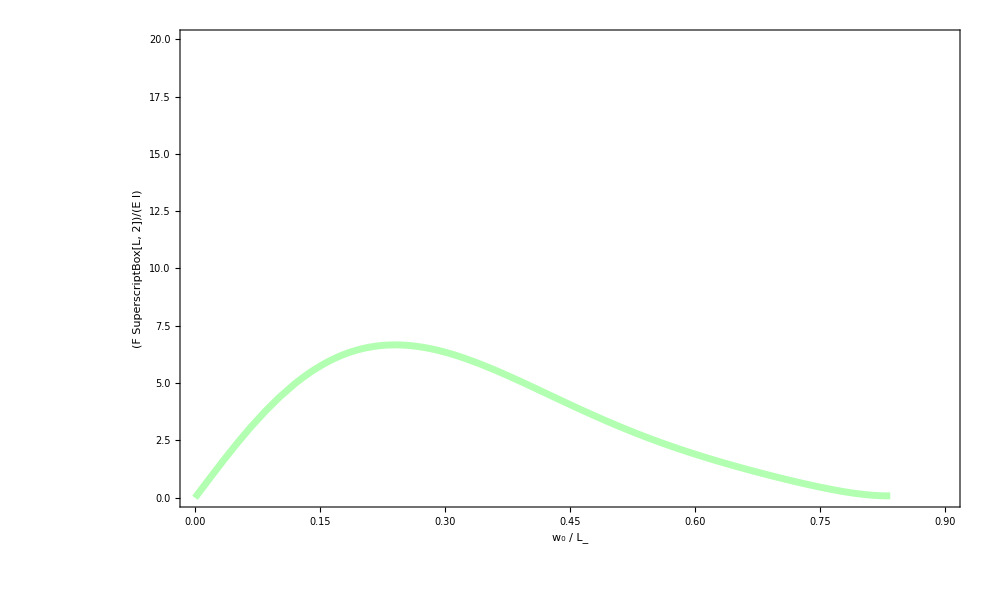

```mathematica
μ0B=0.0;
Posμ0B=μ0B/0.002+1;
Endindex=SolutionVector01[[Posμ0B,-1,1]];
fitFw0B=Module[{data1,fit},
data1=SolutionVector01[[Posμ0B,;;,{1,2}]];
fit[x_]=Fit[data1,{x,x^2,x^3,x^4,x^5,x^6},x];
Function[x,Evaluate@fit[x]]
];
P11=Plot[fitFw0B[x],{x,0,Endindex},PlotStyle->Directive[Dashing[0.01],Gray,Thickness[0.003]],
GridLines->None,Ticks->Automatic,PlotRange->{{0.0,1.0},{0,20}},
PlotLegends->Placed[LineLegend[
{Directive[Dashing[0.01],Gray,Thickness[0.006]],
Directive[Green,Thickness[0.01],Opacity[0.3]]},
{Outline@Style["μ = μ_0",Black(*,Italic*),FontFamily->"Times",TextSize],
Outline@Style["μ = μ_0(1+Â cos((S/λ)+ϕ))",Black(*,Italic*),FontFamily->"Times",TextSize]}],Scaled[{0.8,0.9}]],
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6]
P12=Plot[fitFw0B[x],{x,0,Endindex},PlotStyle->Directive[Green,Thickness[0.005],Opacity[0.3]],
GridLines->None,Ticks->Automatic,PlotRange->{{0.0,0.9},{0,20}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6]
```

### Constant and Sinusoidal μ = 0.5(1+0.2 cos(S/0.02+0))

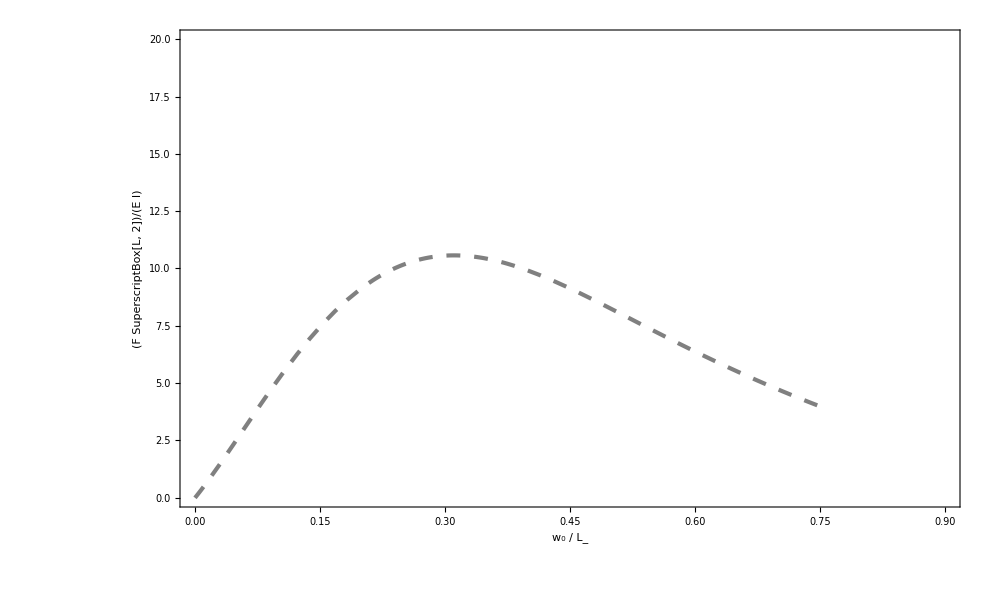

```mathematica
μ0B=0.5;
Abasis =0.1;
λbasis=0.02;
ϕbasis=0;
Posμ0B=μ0B/0.002+1;
Endindex=SolutionVector01[[Posμ0B,-1,1]];
fitFw0B=Module[{data1,fit},
data1=SolutionVector01[[Posμ0B,;;,{1,2}]];
fit[x_]=Fit[data1,{x,x^2,x^3,x^4,x^5,x^6},x];
Function[x,Evaluate@fit[x]]
];
P21=Plot[fitFw0B[x],{x,0,Endindex},PlotStyle->Directive[Dashing[0.01],Gray,Thickness[0.003]],
GridLines->None,Ticks->Automatic,PlotRange->{{0.0,0.9},{0,20}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6]
```

```mathematica
Off[General::partw]
Module[{μ0={μ0B},A = Abasis,λ=λbasis,ϕ=ϕbasis},
arclength=SolutionVector01[[;;,;;,5]];
frictionC=SolutionVector01[[;;,;;,6]];
levelset=frictionC-A Cos[arclength/λ+ϕ];
FwLevelset=Flatten[Table[{SolutionVector01[[i,j,1]],SolutionVector01[[i,j,2]],
levelset[[i,j]]},{i,1,Length@SolutionVector01},{j,1,Length[SolutionVector01[[i]]]}],1];
	Levelμ0=Table[Select[FwLevelset,Abs[#[[3]]-i]<10^-3&],{i,μ0}];
Levelμ0S=(SortBy[Levelμ0[[#]],First])&/@Range@Length@μ0;
(*FailIndex=Length@Select[Levelμ0S[[1,;;,1]],0<#≤w0starN[[NTest]]&]+LengthOffset;*)];
Lfragf[x_,k_,x0_,y0_]=-k(x-x0)+y0;
fitSw0B=Module[{data1,fit},
data1=SolutionVector01[[Posμ0B,;;,{1,5}]];
fit[x_]=Fit[data1,{1,x,x^2,x^3},x];
Function[x,fit[x]]
];
fitVariation=Module[{ λ=λbasis,ϕ=ϕbasis,xx1,yy1,data1,ABF},
xx1=fitSw0B/@Levelμ0S[[1,;;,1]];
yy1=Levelμ0S[[1,;;,2]]-fitFw0B/@Levelμ0S[[1,;;,1]];
data1=Transpose@{xx1,yy1};
ABF=FindFit[data1,(B1 x +B2 x^2 +B3 x^3 +B4 x^4 + B5 x^5+B6 x^6   +B7 x^7 +B8 x^8 )Cos[x/λ+ϕ],{B1,B2,B3,B4,B5,B6,B7,B8},x];
Function[x,Evaluate[(B1 x +B2 x^2 +B3 x^3 +B4 x^4 + B5 x^5 +B6 x^6 +B7 x^7 +B8 x^8 (*+B9 x^9+B10 x^10*) )Cos[x/λ+ϕ]/.ABF]]
];
```

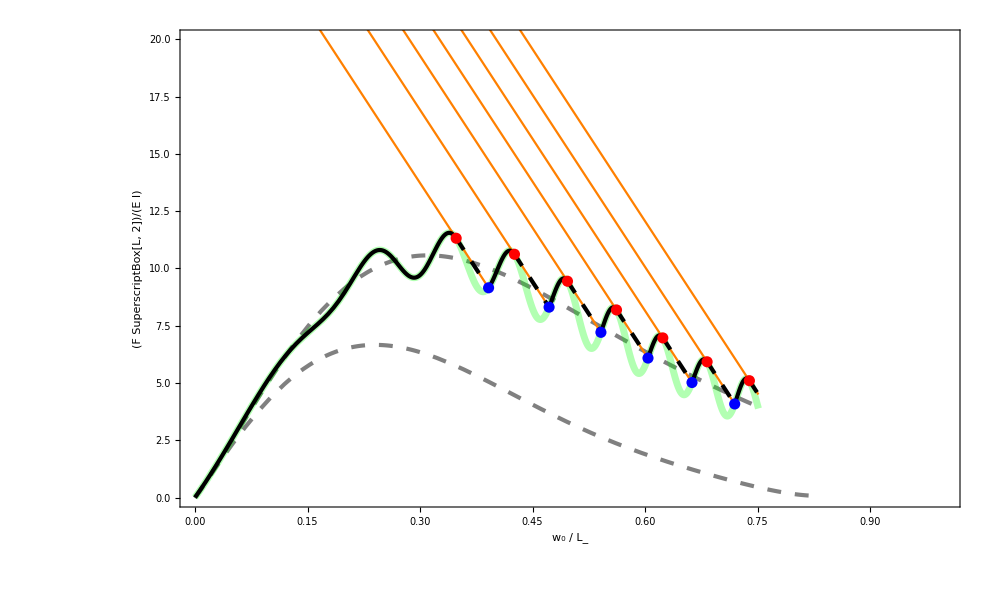

```mathematica
EndFail=Endindex;
P22=Module[{OblSlope=50,f,IntSecPxSol,IntSecPx,IntSecPxy,IntSecP,LIntSecPxSol,LIntSecPx,LIntSecPxy,LIntSecP,Lfrag,LfragArray,LfragRange,ffragRangeFront,ffragRange},
f[x_]=Simplify[Through[(Composition[fitVariation,fitSw0B]+fitFw0B)[x]]];
IntSecPxSol=NSolve[{f'[x]==-OblSlope,0<x<EndFail},x];
IntSecPx=x/.#&/@IntSecPxSol[[;;;;2]];
IntSecPxy={x,f[x]}/.#&/@IntSecPxSol[[;;;;2]];
LIntSecPxSol=(NSolve[{f[x]==Lfragf[x,OblSlope,IntSecPxy[[#,1]],IntSecPxy[[#,2]]],IntSecPxy[[#,1]]+10^-5<x<EndFail},x][[1]])&/@Range[Length@IntSecPxy];
ind=0;
If[LIntSecPxSol[[-1]]=={}[[1]],ind=1;LIntSecPxSol[[-1]]={x->EndFail}];
LIntSecPx=x/.#&/@LIntSecPxSol;
LIntSecPxy={x,f[x]}/.#&/@LIntSecPxSol;
Lfrag[x_]=({Lfragf[x,OblSlope,IntSecPxy[[#,1]],IntSecPxy[[#,2]]],IntSecPx[[#]]<x<LIntSecPx[[#]]})&/@Range@Length@IntSecPx;
ffrag=Simplify@Function[x,Evaluate@Piecewise[Lfrag[x],f[x]]];
(*The below commands are only for plotting*)
IntSecP=Point[IntSecPxy];
LIntSecP=Point[LIntSecPxy[[;;-2]]];
LfragArray=Function[x,Lfragf[x,OblSlope,IntSecPxy[[#,1]],IntSecPxy[[#,2]]]]&/@Range@Length@IntSecPx;
LfragRange={IntSecPx[[#]],LIntSecPx[[#]]}&/@Range@Length@IntSecPx;
ffragRangeFront=Prepend[{LIntSecPx[[#]],IntSecPx[[#+1]]}&/@Range@(Length@LIntSecPx-1),{0,IntSecPx[[1]]}];
If[ind==1,ffragRange=ffragRangeFront,ffragRange=Append[ffragRangeFront,{LIntSecPx[[-1]],EndFail}]];
If[Length@ffragRange==2,ffragRange={{0,EndFail}}];
Show[Plot[{f[x]},{x,0,EndFail},PlotStyle->Directive[Green,Thickness[0.005],Opacity[0.3]],
GridLines->None,Ticks->Automatic,PlotRange->{{0.0,0.9},{0,20}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6]
,Plot[Lfragf[x,OblSlope,IntSecPxy[[#,1]],IntSecPxy[[#,2]]],{x,0,LIntSecPx[[#]]},PlotStyle->{Orange}]&/@Range@Length@IntSecPxy
,Plot[LfragArray[[#]][x],{x,LfragRange[[#,1]],LfragRange[[#,2]]},PlotStyle->{Black,Thickness[0.003],Dashing[0.01]}]&/@Range@Length@LfragArray
,Plot[f[x],{x,#[[1]],#[[2]]},PlotStyle->{Black,Thickness[0.003]}]&/@ffragRange
,Graphics[{Red,PointSize[0.008],IntSecP}]
,Graphics[{Blue,PointSize[0.008],LIntSecP}]
]
(*The above commands are only for plotting*)
];
Show[P11,P21,P22]
```

### Constant and Sinusoidal μ = 0.9(1+0.1 cos(S/0.02+π))

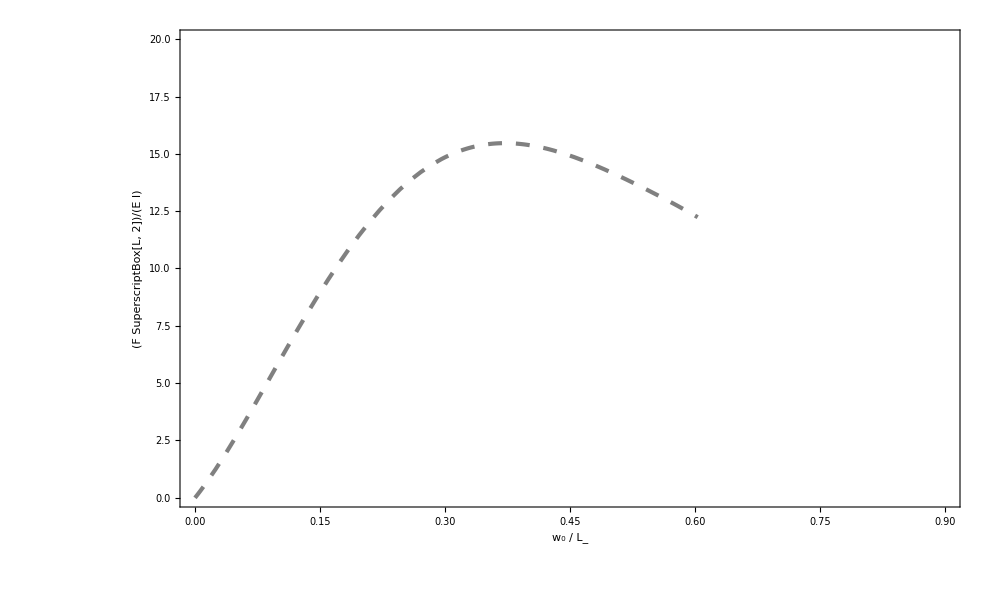

```mathematica
μ0B=0.9;
Abasis =0.09;
λbasis=0.02;
ϕbasis=π;
Posμ0B=μ0B/0.002+1;
Endindex=SolutionVector01[[Posμ0B,-1,1]];
fitFw0B=Module[{data1,fit},
data1=SolutionVector01[[Posμ0B,;;,{1,2}]];
fit[x_]=Fit[data1,{x,x^2,x^3,x^4,x^5,x^6},x];
Function[x,Evaluate@fit[x]]
];
P31=Plot[fitFw0B[x],{x,0,Endindex},PlotStyle->Directive[Dashing[0.01],Gray,Thickness[0.003]],
GridLines->None,Ticks->Automatic,PlotRange->{{0.0,0.9},{0,20}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6]
```

```mathematica
Off[General::partw]
Module[{μ0={μ0B},A = Abasis,λ=λbasis,ϕ=ϕbasis},
arclength=SolutionVector01[[;;,;;,5]];
frictionC=SolutionVector01[[;;,;;,6]];
levelset=frictionC-A Cos[arclength/λ+ϕ];
FwLevelset=Flatten[Table[{SolutionVector01[[i,j,1]],SolutionVector01[[i,j,2]],
levelset[[i,j]]},{i,1,Length@SolutionVector01},{j,1,Length[SolutionVector01[[i]]]}],1];
	Levelμ0=Table[Select[FwLevelset,Abs[#[[3]]-i]<10^-3&],{i,μ0}];
Levelμ0S=(SortBy[Levelμ0[[#]],First])&/@Range@Length@μ0;
(*FailIndex=Length@Select[Levelμ0S[[1,;;,1]],0<#≤w0starN[[NTest]]&]+LengthOffset;*)];
Lfragf[x_,k_,x0_,y0_]=-k(x-x0)+y0;
fitSw0B=Module[{data1,fit},
data1=SolutionVector01[[Posμ0B,;;,{1,5}]];
fit[x_]=Fit[data1,{1,x,x^2,x^3},x];
Function[x,fit[x]]
];
fitVariation=Module[{ λ=λbasis,ϕ=ϕbasis,xx1,yy1,data1,ABF},
xx1=fitSw0B/@Levelμ0S[[1,;;,1]];
yy1=Levelμ0S[[1,;;,2]]-fitFw0B/@Levelμ0S[[1,;;,1]];
data1=Transpose@{xx1,yy1};
ABF=FindFit[data1,(B1 x +B2 x^2 +B3 x^3 +B4 x^4 + B5 x^5+B6 x^6   +B7 x^7 +B8 x^8 )Cos[x/λ+ϕ],{B1,B2,B3,B4,B5,B6,B7,B8},x];
Function[x,Evaluate[(B1 x +B2 x^2 +B3 x^3 +B4 x^4 + B5 x^5 +B6 x^6 +B7 x^7 +B8 x^8 (*+B9 x^9+B10 x^10*) )Cos[x/λ+ϕ]/.ABF]]
];
```

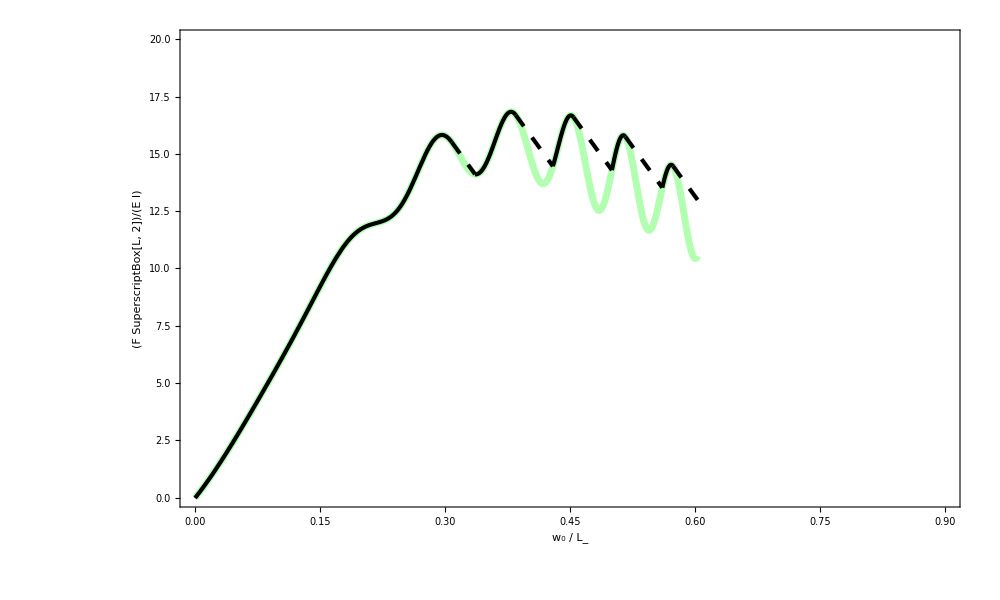

```mathematica
EndFail=Endindex;
P32=Module[{OblSlope=50,f,IntSecPxSol,IntSecPx,IntSecPxy,IntSecP,LIntSecPxSol,LIntSecPx,LIntSecPxy,LIntSecP,Lfrag,LfragArray,LfragRange,ffragRangeFront,ffragRange},
f[x_]=Simplify[Through[(Composition[fitVariation,fitSw0B]+fitFw0B)[x]]];
IntSecPxSol=NSolve[{f'[x]==-OblSlope,0<x<EndFail},x];
IntSecPx=x/.#&/@IntSecPxSol[[;;;;2]];
IntSecPxy={x,f[x]}/.#&/@IntSecPxSol[[;;;;2]];
LIntSecPxSol=(NSolve[{f[x]==Lfragf[x,OblSlope,IntSecPxy[[#,1]],IntSecPxy[[#,2]]],IntSecPxy[[#,1]]+10^-5<x<EndFail},x][[1]])&/@Range[Length@IntSecPxy];
ind=0;
If[LIntSecPxSol[[-1]]=={}[[1]],ind=1;LIntSecPxSol[[-1]]={x->EndFail}];
LIntSecPx=x/.#&/@LIntSecPxSol;
LIntSecPxy={x,f[x]}/.#&/@LIntSecPxSol;
Lfrag[x_]=({Lfragf[x,OblSlope,IntSecPxy[[#,1]],IntSecPxy[[#,2]]],IntSecPx[[#]]<x<LIntSecPx[[#]]})&/@Range@Length@IntSecPx;
ffrag=Simplify@Function[x,Evaluate@Piecewise[Lfrag[x],f[x]]];
(*The below commands are only for plotting*)
IntSecP=Point[IntSecPxy];
LIntSecP=Point[LIntSecPxy[[;;-2]]];
LfragArray=Function[x,Lfragf[x,OblSlope,IntSecPxy[[#,1]],IntSecPxy[[#,2]]]]&/@Range@Length@IntSecPx;
LfragRange={IntSecPx[[#]],LIntSecPx[[#]]}&/@Range@Length@IntSecPx;
ffragRangeFront=Prepend[{LIntSecPx[[#]],IntSecPx[[#+1]]}&/@Range@(Length@LIntSecPx-1),{0,IntSecPx[[1]]}];
If[ind==1,ffragRange=ffragRangeFront,ffragRange=Append[ffragRangeFront,{LIntSecPx[[-1]],EndFail}]];
If[Length@ffragRange==2,ffragRange={{0,EndFail}}];
Show[Plot[{f[x]},{x,0,EndFail},PlotStyle->Directive[Green,Thickness[0.005],Opacity[0.3]],
GridLines->None,Ticks->Automatic,PlotRange->{{0.0,0.9},{0,20}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6]
(*,Plot[Lfragf[x,OblSlope,IntSecPxy[[#,1]],IntSecPxy[[#,2]]],{x,0,LIntSecPx[[#]]},PlotStyle->{Orange}]&/@Range@Length@IntSecPxy
,Graphics[{Red,PointSize[0.008],IntSecP}]
,Graphics[{Blue,PointSize[0.008],LIntSecP}]*)
,Plot[LfragArray[[#]][x],{x,LfragRange[[#,1]],LfragRange[[#,2]]},PlotStyle->{Black,Thickness[0.003],Dashing[0.01]}]&/@Range@Length@LfragArray
,Plot[f[x],{x,#[[1]],#[[2]]},PlotStyle->{Black,Thickness[0.003]}]&/@ffragRange
]
(*The above commands are only for plotting*)
]
```

```mathematica
Outline[text_]:=First@ImportString[ExportString[text,"PDF"],"PDF","TextMode"->"Outlines"]
```

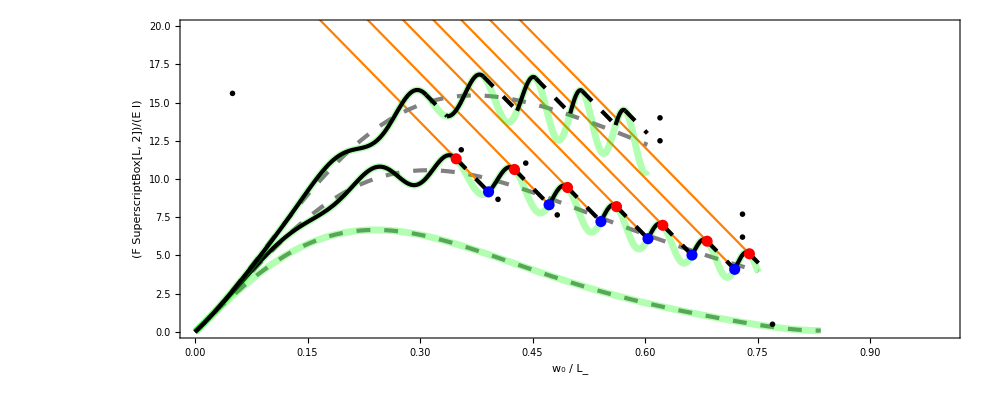

```mathematica
TextPx = 0.8;
TextPy = 15;
TextPyOffSet=1.9;
TextSize=38;
PSche=Show[P11,P12,P21,P22,P31,P32,
Graphics[{Text[Outline@Style["a",Black,FontFamily->"Times",TextSize],{0.355,11.91}],
Text[Outline@Style["b",Black,FontFamily->"Times",TextSize],{0.404,8.67}],
Text[Outline@Style["c",Black,FontFamily->"Times",TextSize],{0.441,11.04}],
Text[Outline@Style["d",Black,FontFamily->"Times",TextSize],{0.483,7.65}],
Text[Outline@Style["μ_0 = "<>ToString[NumberForm[0.0,{3,1}]],Black,FontFamily->"Times",TextSize],{0.77,0.5},{-1,0}],Text[Outline@Style["μ_0 = "<>ToString[NumberForm[0.9,{3,1}]]<>",  Â = "<>ToString[NumberForm[0.1,{3,1}]],Black,FontFamily->"Times",TextSize],{0.62,14},{-1,0}],
Text[Outline@Style["λ = "<>ToString[NumberForm[0.02 ,{3,2}]]<>"L, "<>" ϕ = π",Black,FontFamily->"Times",TextSize],{0.62,14-1.5},{-1,0}],
Text[Outline@Style["μ_0 = "<>ToString[NumberForm[0.5,{3,1}]]<>",  Â = "<>ToString[NumberForm[0.2,{3,1}]],Black,FontFamily->"Times",TextSize],{0.73,6.2+1.5},{-1,0}],
Text[Outline@Style["λ = "<>ToString[NumberForm[0.02 ,{3,2}]]<>"L, "<>" ϕ = "<>ToString[NumberForm[0.0,{3,1}]],Black,FontFamily->"Times",TextSize],{0.73,6.2},{-1,0}],
Text[Outline@Style["-(k_c L^3)/(E I)",Black,FontFamily->"Times",TextSize],{0.05,15.6},{0,0}]}],
AspectRatio->0.4,ImageSize->1000]
```

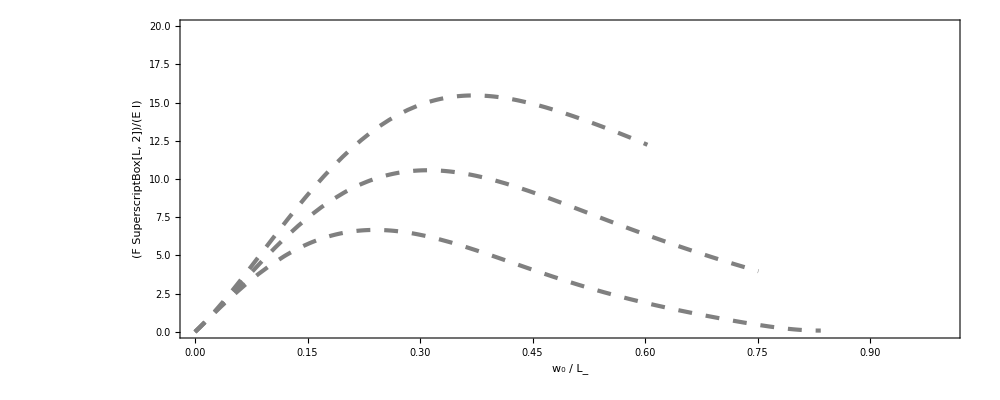

```mathematica
Layer1 = Show[P11,P21,P31,AspectRatio->0.4,ImageSize->1000]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["figure/Layer1.EPS",Layer1]
```

/Users/wenqiangfang/Dropbox (Brown)/Spicule slip/Wfiles

figure/Layer1.EPS

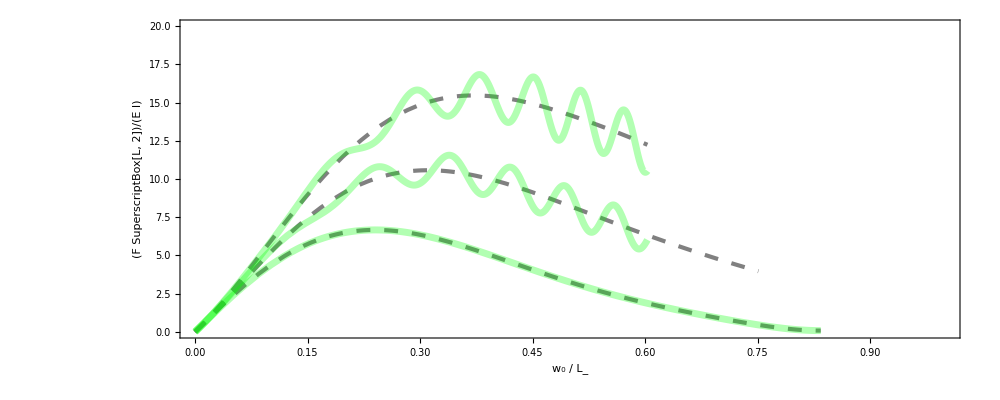

```mathematica
Layer2= Show[P11,P21,P31,P12,P23,P33,AspectRatio->0.4,ImageSize->1000]
```

```mathematica
Export["figure/Layer2.EPS",Layer2]
```

figure/Layer2.EPS

```mathematica
Export["figure/Layer3.EPS",PSche]
```

figure/Layer3.EPS

```mathematica
SetDirectory[NotebookDirectory[]]
Export["figure/Sawtooth_V3.EPS",PSche,ImageSize->1000]
```

/Users/wenqiangfang/Dropbox (Brown)/Spicule slip/Wfiles

figure/Sawtooth_V3.EPS

### μ = 0.5

```mathematica
Pframe=Show@Table[
Module[{nlist=n,data1,k = 5,x,x2,basis,f1,obliqueL1,psol1,TangentP,wsSol,ws,PwCurve,ObliqueLine ,TangentPoint},
data1=ShortSolVect[[nlist,;;,1;;2]];
x2=data1[[-1,1]];
f1[x_]=Fit[data1,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10},x];
obliqueL1[w0_,ws_]=k(ws-w0);
psol1=NSolve[{f1'[x]==-k,0<x<x2},x,Reals];
TangentP={x/.psol1[[1]],f1[x/.psol1[[1]]]};
wsSol=NSolve[obliqueL1[TangentP[[1]],ws]==TangentP[[2]],ws];
PwCurve=ListPlot[data1,Joined->True,PlotStyle->Directive[Black,Thickness[0.005]],ImageSize->Large,
GridLines->None,Ticks->Automatic,PlotRange->{{0.0,0.9},{0,20}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6];
ObliqueLine=Plot[{obliqueL1[x,ws/.wsSol[[1]]]}, {x, 0, TangentP[[1]]}
,PlotStyle->Directive[Dashed,Black,Thickness[0.005]]];
TangentPoint=Graphics[{PointSize[0.015],Red,Point[TangentP]}];
Show[PwCurve,ObliqueLine ,TangentPoint,PlotRange->{{0.0,0.9},{0,20}}]]
,{n,{1,4,6}}];
PExtraOL=Module[{nlist=1,data1,k = 5,x,x2,basis,f1,obliqueL1,psol1,TangentP,wsSol,ws,ObliqueLine ,dis,nOL=3},
data1=ShortSolVect[[nlist,;;,1;;2]];
x2=data1[[-1,1]];
f1[x_]=Fit[data1,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10},x];
obliqueL1[w0_,ws_]=k(ws-w0);
psol1=NSolve[{f1'[x]==-k,0<x<x2},x,Reals];
TangentP={x/.psol1[[1]],f1[x/.psol1[[1]]]};
wsSol=NSolve[obliqueL1[TangentP[[1]],ws]==TangentP[[2]],ws];
dis=(ws/.wsSol[[1]])/nOL;
ObliqueLine=Plot[obliqueL1[x,#*dis]&/@Range@nOL, {x, 0, TangentP[[1]]}
,PlotStyle->Directive[(*Dashing[{0.015,0.02}]*)Dashed,Black,Thickness[0.005]]]];
Pschematic1=Show[Pframe,PExtraOL]
```

### The real path for slope of Test#1

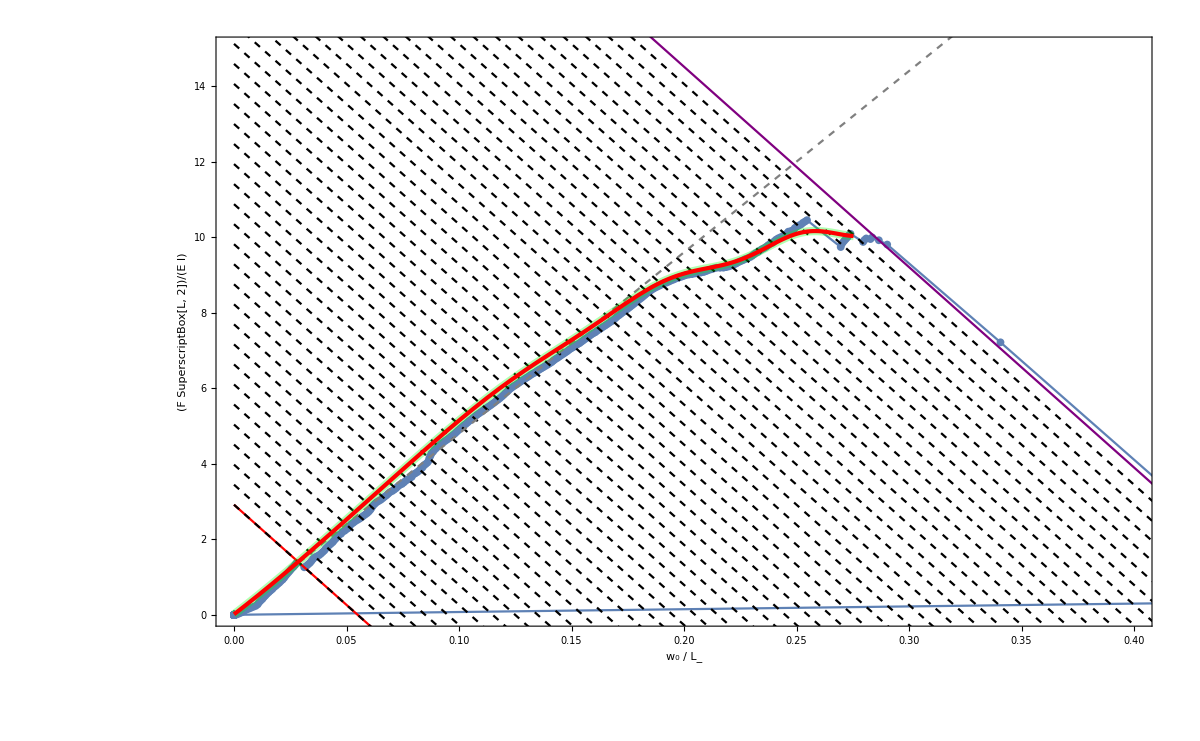

3.76008

```mathematica
EndFailOffset=-0.00;
Pffrag=Module[{f,IntSecPxSol,IntSecPx,IntSecPxy,IntSecP,LIntSecPxSol,LIntSecPx,LIntSecPxy,LIntSecP,Lfrag,LfragArray,LfragRange,ffragRangeFront,ffragRange},
f[x_]=Simplify[Through[(Composition[fitVariation,fitSw0B]+fitFw0B)[x]]];
IntSecPxSol=NSolve[{f'[x]==-OblSlope[[NTest]],0<x<EndFail+EndFailOffset},x];
IntSecPx=x/.#&/@IntSecPxSol[[;;;;2]];
IntSecPxy={x,f[x]}/.#&/@IntSecPxSol[[;;;;2]];
LIntSecPxSol=(NSolve[{f[x]==Lfragf[x,OblSlope[[NTest]],IntSecPxy[[#,1]],IntSecPxy[[#,2]]],IntSecPxy[[#,1]]+10^-5<x<EndFail+EndFailOffset},x][[1]])&/@Range[Length@IntSecPxy];
ind=0;
If[LIntSecPxSol[[-1]]=={}[[1]],ind=1;LIntSecPxSol[[-1]]={x->EndFail+EndFailOffset}];
LIntSecPx=x/.#&/@LIntSecPxSol;
LIntSecPxy={x,f[x]}/.#&/@LIntSecPxSol;
Lfrag[x_]=({Lfragf[x,OblSlope[[NTest]],IntSecPxy[[#,1]],IntSecPxy[[#,2]]],IntSecPx[[#]]<x<LIntSecPx[[#]]})&/@Range@Length@IntSecPx;
ffrag=Simplify@Function[x,Evaluate@Piecewise[Lfrag[x],f[x]]];
(*The below commands are only for plotting*)
IntSecP=Point[IntSecPxy];
LIntSecP=Point[LIntSecPxy];
LfragArray=Function[x,Lfragf[x,OblSlope[[NTest]],IntSecPxy[[#,1]],IntSecPxy[[#,2]]]]&/@Range@Length@IntSecPx;
LfragRange={IntSecPx[[#]],LIntSecPx[[#]]}&/@Range@Length@IntSecPx;
ffragRangeFront=Prepend[{LIntSecPx[[#]],IntSecPx[[#+1]]}&/@Range@(Length@LIntSecPx-1),{0,IntSecPx[[1]]}];
If[ind==1,ffragRange=ffragRangeFront,ffragRange=Append[ffragRangeFront,{LIntSecPx[[-1]],EndFail+EndFailOffset}]];
If[Length@ffragRange==2,ffragRange={{0,EndFail+EndFailOffset}}];
Show[Plot[{f[x],Lfragf[x,OblSlope[[NTest]],#[[1]],#[[2]]]&/@IntSecPxy},{x,0,EndFail+EndFailOffset},PlotRange->{{0,EndFail+EndFailOffset},{0,15}},ImageSize->1000,PlotStyle->{Directive[Green,Thickness[0.005],Opacity[0.3]],Orange}]
(*,Graphics[{Red,PointSize[0.008],IntSecP}]
,Graphics[{Green,PointSize[0.008],LIntSecP}]*)
,Plot[LfragArray[[#]][x],{x,LfragRange[[#,1]],LfragRange[[#,2]]},PlotStyle->{Red,Thickness[0.0025],Dashed}]&/@Range@Length@LfragArray
,Plot[f[x],{x,#[[1]],#[[2]]},PlotStyle->{Red,Thickness[0.0025]}]&/@ffragRange
]
(*The above commands are only for plotting*)
];
Show[
PSingleExp,
Pffrag
]
L2listf=Norm[ffrag/@xx-yy]
```